## Lesson

Histogram:

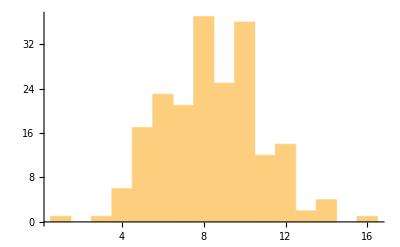

```mathematica
Histogram[StringLength[Take[WordList[],200]]]
```

3D list plot:

```mathematica
ListPlot3D[GeoElevationData[GeoDisk[Entity["Mountain","MountEverest"],Quantity[2, "Miles"]]]]
```

-Graphics3D-

Contour plot for lists:

```mathematica
ListContourPlot[GeoElevationData[GeoDisk[Entity["Mountain","MountEverest"],Quantity[2, "Miles"]]]]
```

-Graphics-

Relief plot:

```mathematica
ReliefPlot[GeoElevationData[GeoDisk[Entity["Mountain","MountEverest"],Quantity[100, "Miles"]]]]
```

-Graphics-

## Questions

Q1. Make a plot with lines joining the squares, the cubes and the 4th powers of integers up to 10.

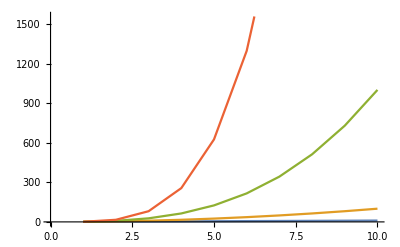

```mathematica
ListLinePlot[Range[10]^#&/@Range[4]]
```

Q2. Make a plot of the first 20 primes, joined by a line, filled to the axis and with a red dot at each prime.

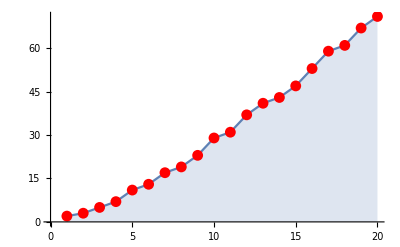

```mathematica
ListLinePlot[Prime[Range[20]],Filling->Axis,Mesh->All,MeshStyle->Red]
```

Q3. Make a 3D plot of the topography for 20 miles around Mount Fuji.

```mathematica
ListPlot3D[GeoElevationData[GeoDisk[Entity["Mountain","FujiSan"],Quantity[20, "Miles"]]]]
```

-Graphics3D-

Q4. Make a relief plot of the topography for 100 miles around Mount Fuji.

```mathematica
ReliefPlot[GeoElevationData[GeoDisk[Entity["Mountain","FujiSan"],Quantity[100, "Miles"]]]]
```

-Graphics-

Q5. Make a 3D plot of heights generated from Mod[i, j] with i and j going up to 100.

```mathematica
ListPlot3D[Table[Mod[i,j],{i,100},{j,100}]]
```

-Graphics3D-

Q6. Make a histogram of the differences between successive primes for the first 10000 primes.

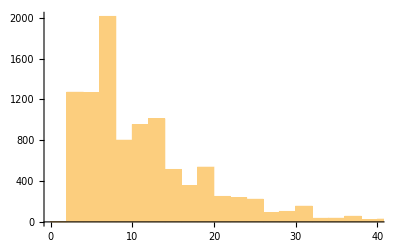

```mathematica
Histogram[Prime[#+1]-Prime[#]&/@Range[10000]]
```

Q7. Make a histogram of the first digits of squares of integers up to 10000 (illustrating Benford’s law).

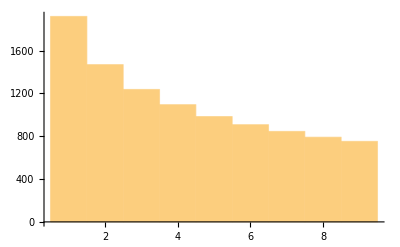

```mathematica
Histogram[IntegerDigits[#^2][[1]]&/@Range[10000]]
```

Q8. Make a histogram of the length of Roman numerals up to 1000.

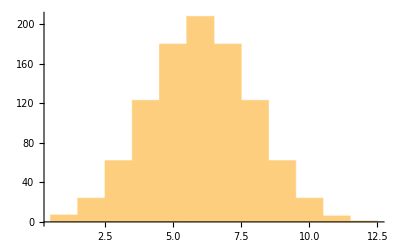

```mathematica
Histogram[StringLength[RomanNumeral[#]]&/@Range[1000]]
```

Q9. Make a histogram of sentence lengths in the Wikipedia article on computers.

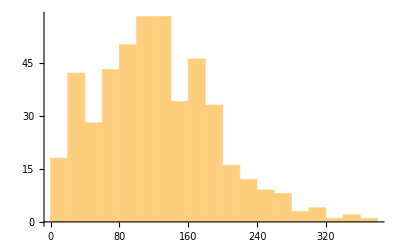

```mathematica
Histogram[StringLength[TextSentences[WikipediaData["computers"]]]]
```

Q10. Make a list of histograms of 10000 instances of totals of n random reals up to 100, with n going from 1 to 5 (illustrating the central limit theorem).

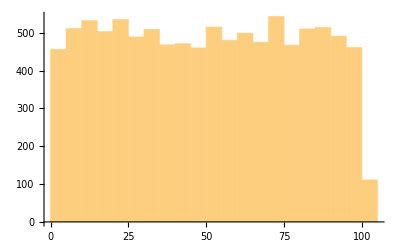
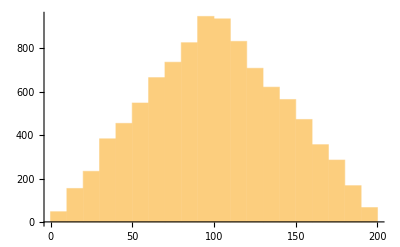
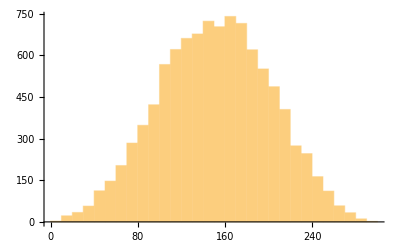
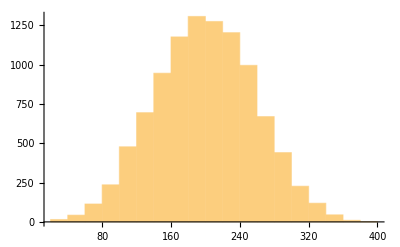
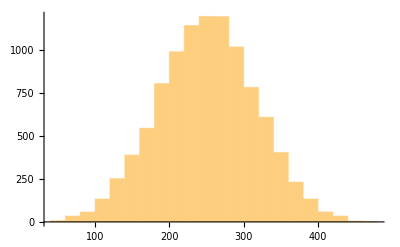

```mathematica
Table[Histogram[Table[Total[RandomInteger[100,n]],10000]],{n,5}]
```

Q11. Generate a 3D list plot using the image data from a binarized size-200 letter “W” as heights.

```mathematica
ListPlot3D[ImageData[Binarize[Rasterize[Style["W",200]]]]]
```

-Graphics3D-

## Extended Questions

+Q1. Make a histogram of word lengths in the Wikipedia article on computers.

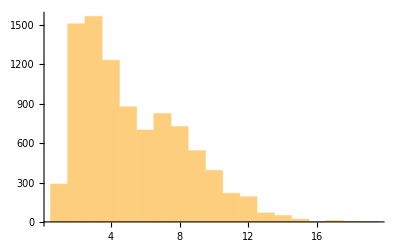

```mathematica
Histogram[StringLength[TextWords[WikipediaData["computers"]]]]
```